## Ising model

### Conformal blocks

```mathematica
SetDirectory[NotebookDirectory[]];
<<MSCB2d`
```

MSCB2d is a Mathematica package that evaluates
Momentum-Space Conformal Blocks in a 2d CFT.

The Wightman 4-point function
  ⟨Ω|O_4(p_4)O_3(p_3)O_2(p_2)O_1(p_1)|Ω⟩
    = (2π)^2 δ(p_1+p_2+p_3+p_4) G(p_a)
admits the conformal block expansion
  G(p_a)=∑_x  λ_(12  x)λ_x34 G_x(p_a)
This package provides explicit expressions for G_x
as a function of the conformal weights (h_a,(h̄)_a) of
the external (1,2,3,4) and exchange (x) operators
and of the momenta p_a.

The following conventions are used for the momenta:
  p_i=p_1   
  p_f=-p_4
  k=p_1+p_2=-p_3-p_4
The 4-point function is identically zero unless
all 3 momenta p_i, p_f and k lie in the future
light-cone.

### Ising data

```mathematica
σ=OperatorΔj[1/8,0]
ϵ=OperatorΔj[1,0]
```

O_(1/16,1/16)

O_(1/2,1/2)

Below one can choose to evaluate one of the next 3 entries corresponding to either of the correlators
⟨σσσσ⟩, ⟨ϵϵϵϵ⟩ or ⟨σϵϵσ⟩.

⟨σσσσ⟩:

```mathematica
Δmax=16;
{O1,O2,O3,O4}={σ,σ,σ,σ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_ss.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

38

⟨σσσσ⟩ taking only the Virasoro descendants of ϵ:

```mathematica
Δmax=30;
{O1,O2,O3,O4}={σ,σ,σ,σ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_sse.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

50

⟨ϵϵϵϵ⟩:

```mathematica
Δmax=20;
{O1,O2,O3,O4}={ϵ,ϵ,ϵ,ϵ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_ee.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

36

⟨ϵσσϵ⟩:

```mathematica
Δmax=16;
{O1,O2,O3,O4}={ϵ,σ,σ,ϵ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_se.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

34

⟨σϵϵσ⟩:

```mathematica
Δmax=16;
{O1,O2,O3,O4}={σ,ϵ,ϵ,σ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_se.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

34

⟨σϵσϵ⟩:

```mathematica
Δmax=16;
{O1,O2,O3,O4}={σ,ϵ,σ,ϵ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_se.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

34

⟨σσϵϵ⟩:

```mathematica
Δmax=20;
{O1,O2,O3,O4}={σ,σ,ϵ,ϵ};
OPEdata1=Select[ToExpression[Import["CFTdata/Ising_ss1.dat"]],First[#]≤Δmax&];
OPEdata2=Select[ToExpression[Import["CFTdata/Ising_ee.dat"]],First[#]≤Δmax&];
OPEdata=Table[If[OPEdata1[[i,1;;2]]==OPEdata2[[i,1;;2]],Join[OPEdata1[[i,1;;2]],{√(OPEdata1[[i,3]]OPEdata2[[i,3]])}],Print["ERROR"];Return[]],{i,Length[OPEdata1]}];
Length[OPEdata]
```

36

### Interactive plots

```mathematica
Wexpansion[pf_,k_,pi_]:=Map[#[[3]]If[#[[2]]==0,GlobalCB[O1,O2,O3,O4,OperatorΔj[#[[1]],0]][-pf,k,pi],GlobalCB[O1,O2,O3,O4,OperatorΔj[#[[1]],#[[2]]]][-pf,k,pi]+GlobalCB[O1,O2,O3,O4,OperatorΔj[#[[1]],-#[[2]]]][-pf,k,pi]]&,OPEdata]
```

```mathematica
WexpansionPlot[pf_,k_,pi_]:=Module[{partialsums},
partialsums=Accumulate[Wexpansion[pf,k,pi]];
If[Last[partialsums]<0,partialsums=-partialsums];
ListLinePlot[partialsums,AspectRatio->1/2,PlotRange->All,AxesLabel->{"# operators","W"},AxesOrigin->{0,0}]
]
```

Example of a convergent OPE:

```mathematica
Wexpansion[MomentumLC[1,0.5],MomentumLC[0.3,0.3],MomentumLC[0.5,1]]//Abs//ListLogPlot
WexpansionPlot[MomentumLC[1,0.5],MomentumLC[0.3,0.3],MomentumLC[0.5,1]]
```

Example of a divergent OPE:

```mathematica
Wexpansion[MomentumLC[1,0.5],MomentumLC[1.1,0.3],MomentumLC[0.5,1]]//Abs//ListLogPlot
WexpansionPlot[MomentumLC[1,0.5],MomentumLC[1.1,0.3],MomentumLC[0.5,1]]
```

```mathematica
lightcone=Graphics[{
LightBlue,
Polygon[{{2,2},{0,0},{-2,2}}],
Blue,Dashed,Thick,
Arrow[{{0,0},{1,1}}],
Text["p^+",{0.95,0.85}],
Arrow[{{0,0},{-1,1}}],
Text["p^-",{-0.95,0.85}]
},BaseStyle->{18,FontFamily->"Latin Modern Roman"},PlotRange->{{-1,1},{-1,1}},ImageSize->600];
printP[p_,label_]:=StringJoin@@Flatten[Table[{label[[i]]," = (",ToString[p[[i,1]]],",",ToString[p[[i,2]]],")  "},{i,Length[p]}]]
Manipulate[
Show[
lightcone,
Graphics[{
Inset[WexpansionPlot[Momentum@@Reverse[pf],Momentum@@Reverse[k],Momentum@@Reverse[pi]],{-0.7,-0.9},{0,0},1.4],
Text[printP[{pi,k-pi,pf-k,-pf},{"p_1","p_2","p_3","p_4"}],{0,-0.2}],
Thick,
Arrow[{{0,0},pi}],
Arrow[{pi,k}],
Arrow[{k,pf}],
Arrow[{pf,{0,0}}],
Thin,Gray,Dashed,
Line[{pi-Last[pi]{1,1},pi+{1,1}}],
Line[{pi-Last[pi]{-1,1},pi+{-1,1}}],
Line[{pf-Last[pf]{1,1},pf+{1,1}}],
Line[{pf-Last[pf]{-1,1},pf+{-1,1}}]
}]
],
{{pi,{0.2,0.4}},{-1,0},{1,1},Locator},
{{pf,{-0.3,0.5}},{-1,0},{1,1},Locator},
{{k,{0.1,0.7}},{-1,0},{1,1},Locator}
]
```

### Other plots for the paper

```mathematica
Δmax=26;
{O1,O2,O3,O4}={σ,σ,σ,σ};
OPEdata=Select[ToExpression[Import["CFTdata/Ising_ss.dat"]],First[#]≤Δmax&];
Length[OPEdata]
```

93

```mathematica
plot[pf_,k_,pi_]:=ListLogPlot[Map[{#}&,{OPEdata[[All,1]],(Times@@k)^(11/4)Abs[Wexpansion[pf,k,pi]]}ᵀ],
PlotStyle->Map[ColorData["Rainbow"][If[#[[1]]>0,(#[[2]])/(#[[1]]),0]]&,OPEdata],
PlotMarkers->"★",
Frame->True,FrameLabel->{"Δ = h^+h̄","λ_(h^)^(h̄) |W_(h^)W_(h̄)| (p^2)^(11/4)"},
BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

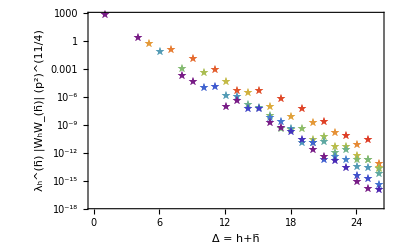

```mathematica
plotconvergent=Show[plot[Momentum[0.9,-0.4],Momentum[0.8,-0.1],Momentum[1.1,0.5]],FrameTicks->{Automatic,Table[{Log[10^n],Superscript[10,n]},{n,2,-20,-6}],None,None}]
```

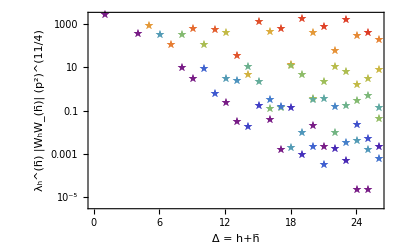

```mathematica
plotdivergent=Show[plot[Momentum[0.9,-0.6],Momentum[1.4,0.3],Momentum[0.9,0.5]],FrameTicks->{Automatic,Table[{Log[10^n],Superscript[10,n]},{n,3,-6,-2}],None,None}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["Ising_convergent.pdf",plotconvergent]
Export["Ising_divergent.pdf",plotdivergent]*)
```